```mathematica
x = 1, 5, 20, 30, 50, 100, 200, 300, 700, 6587
```

Syntax::tsntxi: "x=1,5,20,30,50,100,200,300,700,6587" 不完整；需要更多输入.

```mathematica
Delete x
```

Delete x

```mathematica
data = { {1, 9.7825}, {5, 9.3726}, {20, 8.0777}, {30, 7.3781}, {50, 6.2505}, {100, 4.3696}, {200, 2.3068}, {300, 1.0426}, {700, -2.29}, {6587, -3.1305}};
```

```mathematica
model = a + k / (x - b);
```

```mathematica
fit = FindFit[data, model, {a, k, b}, x]
```

Power::infy: 碰到无穷表达式 1/0..

FindFit::nrlnum: 在 {a,k,b} = {1.,1.,1.} 处，函数值 {ComplexInfinity,-8.1226,-7.02507,-6.34362,-5.23009,-3.3595,-1.30177,-0.0392555,3.29143,4.13065} 不是由实数组成的维度为 {10} 的列表.

```mathematica
FindFit[{{1.0,9.7825},{5.0,9.3726},{20.0,8.0777},{30.0,7.3781},{50.0,6.2505},{100.0,4.3696},{200.0,2.3068},{300.0,1.0426},{700.0,-2.29},{6587.0,-3.1305}},{a+k/(-b+x), {b < 1}},{a,k,b},x];
```

```mathematica
{a,b,k}/.{a->-3.7898999664591617,k->2015.7602028381034,b->-148.5764699665731}
```

{-3.7899,-148.576,2015.76}

```mathematica
{a->-3.7898999664591617,k->2015.7602028381034,b->-148.5764699665731}
```

```mathematica
{a->-3.7898999664591617,k->2015.7602028381034,b->-148.5764699665731}
```

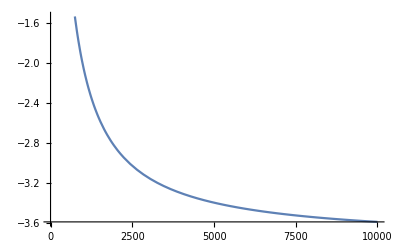

```mathematica
Plot[-3.7898999664591617 +2015.7602028381034 / (x + 148.5764699665731), {x, 0, 10000}]
```

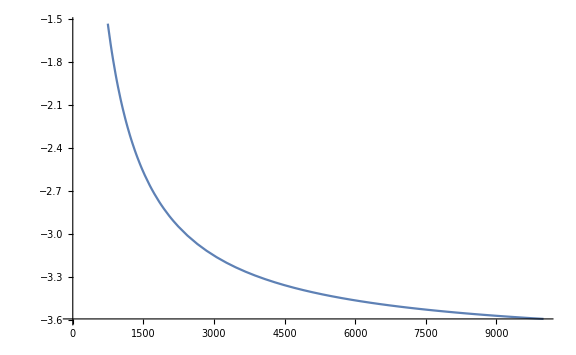

```mathematica
Show[%20,ImageSize->Large]
```

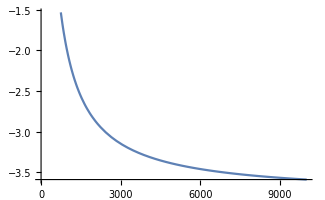

```mathematica
Show[%20,ImageSize->{325,201},AspectRatio->Full]
```

```mathematica
FindFit[{{10,9.88132},{20,9.77365},{30,9.66619},{40,9.55894},{50,9.4519},{60,9.34505},{70,9.23841},{80,9.13196},{90,9.02571},{100,8.91965},{110,8.81378},{120,8.70809},{130,8.60259},{140,8.49727},{150,8.39213},{160,8.28717},{170,8.18238},{180,8.07776},{190,7.97331},{200,7.86903},{210,7.76491},{220,7.66095},{230,7.55716},{240,7.45351},{250,7.35003},{260,7.24669},{270,7.14351},{280,7.04047},{290,6.93758},{300,6.83483},{310,6.73222},{320,6.62975},{330,6.52742},{340,6.42522},{350,6.32315},{360,6.22121},{370,6.11939},{380,6.0177},{390,5.91614},{400,5.81469},{410,5.71336},{420,5.61215},{430,5.51105},{440,5.41006},{450,5.30919},{460,5.20842},{470,5.10775},{480,5.00719},{490,4.90672},{500,4.80636},{510,4.70609},{520,4.60592},{530,4.50584},{540,4.40585},{550,4.30595},{560,4.20613},{570,4.1064},{580,4.00675},{590,3.90718},{600,3.80769},{610,3.70827},{620,3.60893},{630,3.50966},{640,3.41046},{650,3.31133},{660,3.21226},{670,3.11326},{680,3.01432},{690,2.91543},{700,2.81661},{710,2.71784},{720,2.61913},{730,2.52046},{740,2.42185},{750,2.32328},{760,2.22476},{770,2.12629},{780,2.02786},{790,1.92946},{800,1.83111},{810,1.73279},{820,1.6345},{830,1.53625},{840,1.43803},{850,1.33983},{860,1.24166},{870,1.14352},{880,1.0454},{890,0.947299},{900,0.849218},{910,0.751153},{920,0.653103},{930,0.555065},{940,0.457039},{950,0.359022},{960,0.261012},{970,0.163007},{980,0.0650058},{990,-0.0329943},{1000,-0.130994},{1010,-0.22899},{1020,-0.326983},{1030,-0.424969},{1040,-0.522947},{1050,-0.620915},{1060,-0.71887},{1070,-0.816812},{1080,-0.914738},{1090,-1.01265},{1100,-1.11053},{1110,-1.2084},{1120,-1.30624},{1130,-1.40406},{1140,-1.50185},{1150,-1.59961},{1160,-1.69734},{1170,-1.79504},{1180,-1.8927},{1190,-1.99033},{1200,-2.08791},{1210,-2.18546},{1220,-2.28296},{1230,-2.38042},{1240,-2.47783},{1250,-2.5752},{1260,-2.67251},{1270,-2.76977},{1280,-2.86698},{1290,-2.96413},{1300,-3.06123},{1310,-3.15826},{1320,-3.25524},{1330,-3.35215},{1340,-3.449},{1350,-3.54578},{1360,-3.64249},{1370,-3.73913},{1380,-3.8357},{1390,-3.93219},{1400,-4.02861},{1410,-4.12496},{1420,-4.22122},{1430,-4.3174},{1440,-4.4135},{1450,-4.50951},{1460,-4.60544},{1470,-4.70128},{1480,-4.79703},{1490,-4.89268},{1500,-4.98825},{1510,-5.08372},{1520,-5.17909},{1530,-5.27436},{1540,-5.36953},{1550,-5.4646},{1560,-5.55957},{1570,-5.65443},{1580,-5.74919},{1590,-5.84383},{1600,-5.93837},{1610,-6.03279},{1620,-6.1271},{1630,-6.22129},{1640,-6.31537},{1650,-6.40933},{1660,-6.50316},{1670,-6.59688},{1680,-6.69047},{1690,-6.78394},{1700,-6.87728},{1710,-6.97049},{1720,-7.06358},{1730,-7.15653},{1740,-7.24934},{1750,-7.34203},{1760,-7.43458},{1770,-7.52699},{1780,-7.61926},{1790,-7.71139},{1800,-7.80338},{1810,-7.89523},{1820,-7.98693},{1830,-8.07848},{1840,-8.16989},{1850,-8.26115},{1860,-8.35225},{1870,-8.44321},{1880,-8.53401},{1890,-8.62466},{1900,-8.71515},{1910,-8.80548},{1920,-8.89566},{1930,-8.98567},{1940,-9.07553},{1950,-9.16522},{1960,-9.25474},{1970,-9.3441},{1980,-9.43329},{1990,-9.52232},{2000,-9.61118},{2010,-9.69986},{2020,-9.78838},{2030,-9.87672},{2040,-9.96488},{2050,-10.0529},{2060,-10.1407},{2070,-10.2283},{2080,-10.3158},{2090,-10.4031},{2100,-10.4902},{2110,-10.5771},{2120,-10.6638},{2130,-10.7503},{2140,-10.8367},{2150,-10.9229},{2160,-11.0089},{2170,-11.0947},{2180,-11.1803},{2190,-11.2657},{2200,-11.3509},{2210,-11.4359},{2220,-11.5208},{2230,-11.6054},{2240,-11.6898},{2250,-11.7741},{2260,-11.8581},{2270,-11.942},{2280,-12.0256},{2290,-12.1091},{2300,-12.1923},{2310,-12.2754},{2320,-12.3582},{2330,-12.4408},{2340,-12.5233},{2350,-12.6055},{2360,-12.6875},{2370,-12.7693},{2380,-12.8509},{2390,-12.9323},{2400,-13.0135},{2410,-13.0945},{2420,-13.1752},{2430,-13.2558},{2440,-13.3361},{2450,-13.4162},{2460,-13.4961},{2470,-13.5758},{2480,-13.6553},{2490,-13.7345},{2500,-13.8136},{2510,-13.8924},{2520,-13.971},{2530,-14.0494},{2540,-14.1275},{2550,-14.2055},{2560,-14.2832},{2570,-14.3607},{2580,-14.438},{2590,-14.515},{2600,-14.5919},{2610,-14.6685},{2620,-14.7449},{2630,-14.821},{2640,-14.8969},{2650,-14.9727},{2660,-15.0481},{2670,-15.1234},{2680,-15.1984},{2690,-15.2732},{2700,-15.3478},{2710,-15.4221},{2720,-15.4962},{2730,-15.5701},{2740,-15.6438},{2750,-15.7172},{2760,-15.7904},{2770,-15.8634},{2780,-15.9361},{2790,-16.0086},{2800,-16.0809},{2810,-16.1529},{2820,-16.2247},{2830,-16.2963},{2840,-16.3676},{2850,-16.4387},{2860,-16.5096},{2870,-16.5802},{2880,-16.6506},{2890,-16.7208},{2900,-16.7907},{2910,-16.8604},{2920,-16.9299},{2930,-16.9991},{2940,-17.0681},{2950,-17.1369},{2960,-17.2054},{2970,-17.2737},{2980,-17.3418},{2990,-17.4096},{3000,-17.4772},{3010,-17.5445},{3020,-17.6116},{3030,-17.6785},{3040,-17.7451},{3050,-17.8116},{3060,-17.8777},{3070,-17.9437},{3080,-18.0093},{3090,-18.0748},{3100,-18.14},{3110,-18.205},{3120,-18.2698},{3130,-18.3343},{3140,-18.3986},{3150,-18.4626},{3160,-18.5264},{3170,-18.59},{3180,-18.6533},{3190,-18.7164},{3200,-18.7793},{3210,-18.8419},{3220,-18.9043},{3230,-18.9665},{3240,-19.0284},{3250,-19.0901},{3260,-19.1515},{3270,-19.2127},{3280,-19.2737},{3290,-19.3345},{3300,-19.395},{3310,-19.4553},{3320,-19.5153},{3330,-19.5751},{3340,-19.6347},{3350,-19.694},{3360,-19.7531},{3370,-19.812},{3380,-19.8707},{3390,-19.9291},{3400,-19.9872},{3410,-20.0452},{3420,-20.1029},{3430,-20.1604},{3440,-20.2176},{3450,-20.2747},{3460,-20.3315},{3470,-20.388},{3480,-20.4443},{3490,-20.5004},{3500,-20.5563},{3510,-20.612},{3520,-20.6674},{3530,-20.7225},{3540,-20.7775},{3550,-20.8322},{3560,-20.8867},{3570,-20.941},{3580,-20.995},{3590,-21.0489},{3600,-21.1025},{3610,-21.1558},{3620,-21.209},{3630,-21.2619},{3640,-21.3146},{3650,-21.367},{3660,-21.4193},{3670,-21.4713},{3680,-21.5231},{3690,-21.5747},{3700,-21.626},{3710,-21.6772},{3720,-21.7281},{3730,-21.7788},{3740,-21.8292},{3750,-21.8795},{3760,-21.9295},{3770,-21.9793},{3780,-22.0289},{3790,-22.0783},{3800,-22.1275},{3810,-22.1764},{3820,-22.2251},{3830,-22.2736},{3840,-22.3219},{3850,-22.37},{3860,-22.4179},{3870,-22.4655},{3880,-22.5129},{3890,-22.5602},{3900,-22.6072},{3910,-22.654},{3920,-22.7005},{3930,-22.7469},{3940,-22.7931},{3950,-22.839},{3960,-22.8848},{3970,-22.9303},{3980,-22.9756},{3990,-23.0208},{4000,-23.0657},{4010,-23.1104},{4020,-23.1549},{4030,-23.1992},{4040,-23.2433},{4050,-23.2871},{4060,-23.3308},{4070,-23.3743},{4080,-23.4176},{4090,-23.4606},{4100,-23.5035},{4110,-23.5462},{4120,-23.5886},{4130,-23.6309},{4140,-23.673},{4150,-23.7148},{4160,-23.7565},{4170,-23.798},{4180,-23.8393},{4190,-23.8804},{4200,-23.9212},{4210,-23.9619},{4220,-24.0024},{4230,-24.0427},{4240,-24.0828},{4250,-24.1227},{4260,-24.1625},{4270,-24.202},{4280,-24.2413},{4290,-24.2805},{4300,-24.3195},{4310,-24.3582},{4320,-24.3968},{4330,-24.4352},{4340,-24.4734},{4350,-24.5114},{4360,-24.5493},{4370,-24.5869},{4380,-24.6244},{4390,-24.6617},{4400,-24.6988},{4410,-24.7357},{4420,-24.7724},{4430,-24.809},{4440,-24.8453},{4450,-24.8815},{4460,-24.9175},{4470,-24.9534},{4480,-24.989},{4490,-25.0245},{4500,-25.0598},{4510,-25.0949},{4520,-25.1299},{4530,-25.1646},{4540,-25.1992},{4550,-25.2336},{4560,-25.2679},{4570,-25.302},{4580,-25.3359},{4590,-25.3696},{4600,-25.4032},{4610,-25.4366},{4620,-25.4698},{4630,-25.5028},{4640,-25.5357},{4650,-25.5684},{4660,-25.601},{4670,-25.6334},{4680,-25.6656},{4690,-25.6976},{4700,-25.7295},{4710,-25.7613},{4720,-25.7928},{4730,-25.8242},{4740,-25.8555},{4750,-25.8865},{4760,-25.9174},{4770,-25.9482},{4780,-25.9788},{4790,-26.0092},{4800,-26.0395},{4810,-26.0696},{4820,-26.0996},{4830,-26.1294},{4840,-26.1591},{4850,-26.1886},{4860,-26.2179},{4870,-26.2471},{4880,-26.2762},{4890,-26.305},{4900,-26.3338},{4910,-26.3624},{4920,-26.3908},{4930,-26.4191},{4940,-26.4472},{4950,-26.4752},{4960,-26.5031},{4970,-26.5307},{4980,-26.5583},{4990,-26.5857},{5000,-26.6129},{5010,-26.6401},{5020,-26.667},{5030,-26.6938},{5040,-26.7205},{5050,-26.7471},{5060,-26.7735},{5070,-26.7997},{5080,-26.8258},{5090,-26.8518},{5100,-26.8776},{5110,-26.9033},{5120,-26.9289},{5130,-26.9543},{5140,-26.9796},{5150,-27.0048},{5160,-27.0298},{5170,-27.0546},{5180,-27.0794},{5190,-27.104},{5200,-27.1285},{5210,-27.1528},{5220,-27.177},{5230,-27.2011},{5240,-27.2251},{5250,-27.2489},{5260,-27.2726},{5270,-27.2961},{5280,-27.3196},{5290,-27.3429},{5300,-27.3661},{5310,-27.3891},{5320,-27.412},{5330,-27.4348},{5340,-27.4575},{5350,-27.4801},{5360,-27.5025},{5370,-27.5248},{5380,-27.547},{5390,-27.5691},{5400,-27.591},{5410,-27.6128},{5420,-27.6345},{5430,-27.6561},{5440,-27.6776},{5450,-27.6989},{5460,-27.7201},{5470,-27.7412},{5480,-27.7622},{5490,-27.7831},{5500,-27.8038},{5510,-27.8245},{5520,-27.845},{5530,-27.8654},{5540,-27.8857},{5550,-27.9059},{5560,-27.926},{5570,-27.946},{5580,-27.9658},{5590,-27.9856},{5600,-28.0052},{5610,-28.0247},{5620,-28.0441},{5630,-28.0634},{5640,-28.0826},{5650,-28.1017},{5660,-28.1207},{5670,-28.1396},{5680,-28.1583},{5690,-28.177},{5700,-28.1956},{5710,-28.214},{5720,-28.2324},{5730,-28.2506},{5740,-28.2688},{5750,-28.2868},{5760,-28.3047},{5770,-28.3226},{5780,-28.3403},{5790,-28.3579},{5800,-28.3755},{5810,-28.3929},{5820,-28.4103},{5830,-28.4275},{5840,-28.4446},{5850,-28.4617},{5860,-28.4786},{5870,-28.4955},{5880,-28.5123},{5890,-28.5289},{5900,-28.5455},{5910,-28.562},{5920,-28.5783},{5930,-28.5946},{5940,-28.6108},{5950,-28.6269},{5960,-28.6429},{5970,-28.6588},{5980,-28.6747},{5990,-28.6904},{6000,-28.7061},{6010,-28.7216},{6020,-28.7371},{6030,-28.7525},{6040,-28.7677},{6050,-28.7829},{6060,-28.7981},{6070,-28.8131},{6080,-28.828},{6090,-28.8429},{6100,-28.8577},{6110,-28.8723},{6120,-28.8869},{6130,-28.9015},{6140,-28.9159},{6150,-28.9302},{6160,-28.9445},{6170,-28.9587},{6180,-28.9728},{6190,-28.9868},{6200,-29.0008},{6210,-29.0146},{6220,-29.0284},{6230,-29.0421},{6240,-29.0557},{6250,-29.0693},{6260,-29.0827},{6270,-29.0961},{6280,-29.1094},{6290,-29.1226},{6300,-29.1358},{6310,-29.1489},{6320,-29.1619},{6330,-29.1748},{6340,-29.1876},{6350,-29.2004},{6360,-29.2131},{6370,-29.2257},{6380,-29.2383},{6390,-29.2508},{6400,-29.2632},{6410,-29.2755},{6420,-29.2878},{6430,-29.3},{6440,-29.3121},{6450,-29.3241},{6460,-29.3361},{6470,-29.348},{6480,-29.3599},{6490,-29.3716},{6500,-29.3833},{6510,-29.395},{6520,-29.4065},{6530,-29.418},{6540,-29.4294},{6550,-29.4408},{6560,-29.4521},{6570,-29.4633},{6580,-29.4745},{6590,-29.4856},{6600,-29.4966},{6610,-29.5076},{6620,-29.5185},{6630,-29.5293},{6640,-29.5401},{6650,-29.5508},{6660,-29.5614},{6670,-29.572},{6680,-29.5826},{6690,-29.593},{6700,-29.6034},{6710,-29.6137},{6720,-29.624},{6730,-29.6342},{6740,-29.6444},{6750,-29.6545},{6760,-29.6645},{6770,-29.6745},{6780,-29.6844},{6790,-29.6943},{6800,-29.7041},{6810,-29.7138},{6820,-29.7235},{6830,-29.7331},{6840,-29.7427},{6850,-29.7522},{6860,-29.7617},{6870,-29.7711},{6880,-29.7804},{6890,-29.7897},{6900,-29.7989},{6910,-29.8081},{6920,-29.8172},{6930,-29.8263},{6940,-29.8353},{6950,-29.8443},{6960,-29.8532},{6970,-29.862},{6980,-29.8708},{6990,-29.8796},{7000,-29.8883},{7010,-29.8969},{7020,-29.9055},{7030,-29.9141},{7040,-29.9225},{7050,-29.931},{7060,-29.9394},{7070,-29.9477},{7080,-29.956},{7090,-29.9643},{7100,-29.9724},{7110,-29.9806},{7120,-29.9887},{7130,-29.9967},{7140,-30.0047},{7150,-30.0127},{7160,-30.0206},{7170,-30.0284},{7180,-30.0362},{7190,-30.044},{7200,-30.0517},{7210,-30.0594},{7220,-30.067},{7230,-30.0746},{7240,-30.0821},{7250,-30.0896},{7260,-30.097},{7270,-30.1044},{7280,-30.1118},{7290,-30.1191},{7300,-30.1264},{7310,-30.1336},{7320,-30.1408},{7330,-30.1479},{7340,-30.155},{7350,-30.162},{7360,-30.169},{7370,-30.176},{7380,-30.1829},{7390,-30.1898},{7400,-30.1967},{7410,-30.2035},{7420,-30.2102},{7430,-30.2169},{7440,-30.2236},{7450,-30.2302},{7460,-30.2368},{7470,-30.2434},{7480,-30.2499},{7490,-30.2564},{7500,-30.2628},{7510,-30.2692},{7520,-30.2756},{7530,-30.2819},{7540,-30.2882},{7550,-30.2944},{7560,-30.3006},{7570,-30.3068},{7580,-30.3129},{7590,-30.319},{7600,-30.3251},{7610,-30.3311},{7620,-30.3371},{7630,-30.343},{7640,-30.349},{7650,-30.3548},{7660,-30.3607},{7670,-30.3665},{7680,-30.3723},{7690,-30.378},{7700,-30.3837},{7710,-30.3894},{7720,-30.395},{7730,-30.4006},{7740,-30.4062},{7750,-30.4117},{7760,-30.4172},{7770,-30.4227},{7780,-30.4281},{7790,-30.4335},{7800,-30.4389},{7810,-30.4442},{7820,-30.4495},{7830,-30.4548},{7840,-30.46},{7850,-30.4652},{7860,-30.4704},{7870,-30.4755},{7880,-30.4806},{7890,-30.4857},{7900,-30.4908},{7910,-30.4958},{7920,-30.5008},{7930,-30.5057},{7940,-30.5106},{7950,-30.5155},{7960,-30.5204},{7970,-30.5252},{7980,-30.53},{7990,-30.5348},{8000,-30.5396},{8010,-30.5443},{8020,-30.549},{8030,-30.5537},{8040,-30.5583},{8050,-30.5629},{8060,-30.5675},{8070,-30.572},{8080,-30.5765},{8090,-30.581},{8100,-30.5855},{8110,-30.5899},{8120,-30.5944},{8130,-30.5987},{8140,-30.6031},{8150,-30.6074},{8160,-30.6117},{8170,-30.616},{8180,-30.6203},{8190,-30.6245},{8200,-30.6287},{8210,-30.6329},{8220,-30.637},{8230,-30.6412},{8240,-30.6453},{8250,-30.6493},{8260,-30.6534},{8270,-30.6574},{8280,-30.6614},{8290,-30.6654},{8300,-30.6693},{8310,-30.6733},{8320,-30.6772},{8330,-30.6811},{8340,-30.6849},{8350,-30.6887},{8360,-30.6926},{8370,-30.6963},{8380,-30.7001},{8390,-30.7038},{8400,-30.7076},{8410,-30.7113},{8420,-30.7149},{8430,-30.7186},{8440,-30.7222},{8450,-30.7258},{8460,-30.7294},{8470,-30.733},{8480,-30.7365},{8490,-30.74},{8500,-30.7435},{8510,-30.747},{8520,-30.7504},{8530,-30.7539},{8540,-30.7573},{8550,-30.7607},{8560,-30.764},{8570,-30.7674},{8580,-30.7707},{8590,-30.774},{8600,-30.7773},{8610,-30.7806},{8620,-30.7838},{8630,-30.787},{8640,-30.7903},{8650,-30.7934},{8660,-30.7966},{8670,-30.7998},{8680,-30.8029},{8690,-30.806},{8700,-30.8091},{8710,-30.8122},{8720,-30.8152},{8730,-30.8182},{8740,-30.8213},{8750,-30.8243},{8760,-30.8272},{8770,-30.8302},{8780,-30.8331},{8790,-30.8361},{8800,-30.839},{8810,-30.8418},{8820,-30.8447},{8830,-30.8476},{8840,-30.8504},{8850,-30.8532},{8860,-30.856},{8870,-30.8588},{8880,-30.8616},{8890,-30.8643},{8900,-30.8671},{8910,-30.8698},{8920,-30.8725},{8930,-30.8751},{8940,-30.8778},{8950,-30.8805},{8960,-30.8831},{8970,-30.8857},{8980,-30.8883},{8990,-30.8909},{9000,-30.8935},{9010,-30.896},{9020,-30.8986},{9030,-30.9011},{9040,-30.9036},{9050,-30.9061},{9060,-30.9085},{9070,-30.911},{9080,-30.9134},{9090,-30.9159},{9100,-30.9183},{9110,-30.9207},{9120,-30.9231},{9130,-30.9254},{9140,-30.9278},{9150,-30.9301},{9160,-30.9325},{9170,-30.9348},{9180,-30.9371},{9190,-30.9394},{9200,-30.9416},{9210,-30.9439},{9220,-30.9461},{9230,-30.9484},{9240,-30.9506},{9250,-30.9528},{9260,-30.955},{9270,-30.9571},{9280,-30.9593},{9290,-30.9614},{9300,-30.9636},{9310,-30.9657},{9320,-30.9678},{9330,-30.9699},{9340,-30.972},{9350,-30.974},{9360,-30.9761},{9370,-30.9781},{9380,-30.9802},{9390,-30.9822},{9400,-30.9842},{9410,-30.9862},{9420,-30.9882},{9430,-30.9901},{9440,-30.9921},{9450,-30.994},{9460,-30.996},{9470,-30.9979},{9480,-30.9998},{9490,-31.0017},{9500,-31.0036},{9510,-31.0054},{9520,-31.0073},{9530,-31.0091},{9540,-31.011},{9550,-31.0128},{9560,-31.0146},{9570,-31.0164},{9580,-31.0182},{9590,-31.02},{9600,-31.0218},{9610,-31.0235},{9620,-31.0253},{9630,-31.027},{9640,-31.0288},{9650,-31.0305},{9660,-31.0322},{9670,-31.0339},{9680,-31.0356},{9690,-31.0372},{9700,-31.0389},{9710,-31.0405},{9720,-31.0422},{9730,-31.0438},{9740,-31.0454},{9750,-31.0471},{9760,-31.0487},{9770,-31.0503},{9780,-31.0518},{9790,-31.0534},{9800,-31.055},{9810,-31.0565},{9820,-31.0581},{9830,-31.0596},{9840,-31.0611},{9850,-31.0627},{9860,-31.0642},{9870,-31.0657},{9880,-31.0672},{9890,-31.0686},{9900,-31.0701},{9910,-31.0716},{9920,-31.073},{9930,-31.0745},{9940,-31.0759},{9950,-31.0773},{9960,-31.0787},{9970,-31.0801},{9980,-31.0815},{9990,-31.0829},{10000,-31.0843}},{a+k/(-b+x),{b<1}},{a,k,b},x];
```

```mathematica
{a->-46.806879857899425,k->171219.36032771305,b->-2810.2409051125132}
```

{a→-46.8069,k→171219.,b→-2810.24}

```mathematica
FindFit[{{10,9.88132},{20,9.77365},{30,9.66619},{40,9.55894},{50,9.4519},{60,9.34505},{70,9.23841},{80,9.13196},{90,9.02571},{100,8.91965},{110,8.81378},{120,8.70809},{130,8.60259},{140,8.49727},{150,8.39213},{160,8.28717},{170,8.18238},{180,8.07776},{190,7.97331},{200,7.86903},{210,7.76491},{220,7.66095},{230,7.55716},{240,7.45351},{250,7.35003},{260,7.24669},{270,7.14351},{280,7.04047},{290,6.93758},{300,6.83483},{310,6.73222},{320,6.62975},{330,6.52742},{340,6.42522},{350,6.32315},{360,6.22121},{370,6.11939},{380,6.0177},{390,5.91614},{400,5.81469},{410,5.71336},{420,5.61215},{430,5.51105},{440,5.41006},{450,5.30919},{460,5.20842},{470,5.10775},{480,5.00719},{490,4.90672},{500,4.80636},{510,4.70609},{520,4.60592},{530,4.50584},{540,4.40585},{550,4.30595},{560,4.20613},{570,4.1064},{580,4.00675},{590,3.90718},{600,3.80769},{610,3.70827},{620,3.60893},{630,3.50966},{640,3.41046},{650,3.31133},{660,3.21226},{670,3.11326},{680,3.01432},{690,2.91543},{700,2.81661},{710,2.71784},{720,2.61913},{730,2.52046},{740,2.42185},{750,2.32328},{760,2.22476},{770,2.12629},{780,2.02786},{790,1.92946},{800,1.83111},{810,1.73279},{820,1.6345},{830,1.53625},{840,1.43803},{850,1.33983},{860,1.24166},{870,1.14352},{880,1.0454},{890,0.947299},{900,0.849218},{910,0.751153},{920,0.653103},{930,0.555065},{940,0.457039},{950,0.359022},{960,0.261012},{970,0.163007},{980,0.0650058},{990,-0.0329943},{1000,-0.130994},{1010,-0.22899},{1020,-0.326983},{1030,-0.424969},{1040,-0.522947},{1050,-0.620915},{1060,-0.71887},{1070,-0.816812},{1080,-0.914738},{1090,-1.01265},{1100,-1.11053},{1110,-1.2084},{1120,-1.30624},{1130,-1.40406},{1140,-1.50185},{1150,-1.59961},{1160,-1.69734},{1170,-1.79504},{1180,-1.8927},{1190,-1.99033},{1200,-2.08791},{1210,-2.18546},{1220,-2.28296},{1230,-2.38042},{1240,-2.47783},{1250,-2.5752},{1260,-2.67251},{1270,-2.76977},{1280,-2.86698},{1290,-2.96413},{1300,-3.06123},{1310,-3.15826},{1320,-3.25524},{1330,-3.35215},{1340,-3.449},{1350,-3.54578},{1360,-3.64249},{1370,-3.73913},{1380,-3.8357},{1390,-3.93219},{1400,-4.02861},{1410,-4.12496},{1420,-4.22122},{1430,-4.3174},{1440,-4.4135},{1450,-4.50951},{1460,-4.60544},{1470,-4.70128},{1480,-4.79703},{1490,-4.89268},{1500,-4.98825},{1510,-5.08372},{1520,-5.17909},{1530,-5.27436},{1540,-5.36953},{1550,-5.4646},{1560,-5.55957},{1570,-5.65443},{1580,-5.74919},{1590,-5.84383},{1600,-5.93837},{1610,-6.03279},{1620,-6.1271},{1630,-6.22129},{1640,-6.31537},{1650,-6.40933},{1660,-6.50316},{1670,-6.59688},{1680,-6.69047},{1690,-6.78394},{1700,-6.87728},{1710,-6.97049},{1720,-7.06358},{1730,-7.15653},{1740,-7.24934},{1750,-7.34203},{1760,-7.43458},{1770,-7.52699},{1780,-7.61926},{1790,-7.71139},{1800,-7.80338},{1810,-7.89523},{1820,-7.98693},{1830,-8.07848},{1840,-8.16989},{1850,-8.26115},{1860,-8.35225},{1870,-8.44321},{1880,-8.53401},{1890,-8.62466},{1900,-8.71515},{1910,-8.80548},{1920,-8.89566},{1930,-8.98567},{1940,-9.07553},{1950,-9.16522},{1960,-9.25474},{1970,-9.3441},{1980,-9.43329},{1990,-9.52232},{2000,-9.61118},{2010,-9.69986},{2020,-9.78838},{2030,-9.87672},{2040,-9.96488},{2050,-10.0529},{2060,-10.1407},{2070,-10.2283},{2080,-10.3158},{2090,-10.4031},{2100,-10.4902},{2110,-10.5771},{2120,-10.6638},{2130,-10.7503},{2140,-10.8367},{2150,-10.9229},{2160,-11.0089},{2170,-11.0947},{2180,-11.1803},{2190,-11.2657},{2200,-11.3509},{2210,-11.4359},{2220,-11.5208},{2230,-11.6054},{2240,-11.6898},{2250,-11.7741},{2260,-11.8581},{2270,-11.942},{2280,-12.0256},{2290,-12.1091},{2300,-12.1923},{2310,-12.2754},{2320,-12.3582},{2330,-12.4408},{2340,-12.5233},{2350,-12.6055},{2360,-12.6875},{2370,-12.7693},{2380,-12.8509},{2390,-12.9323},{2400,-13.0135},{2410,-13.0945},{2420,-13.1752},{2430,-13.2558},{2440,-13.3361},{2450,-13.4162},{2460,-13.4961},{2470,-13.5758},{2480,-13.6553},{2490,-13.7345},{2500,-13.8136},{2510,-13.8924},{2520,-13.971},{2530,-14.0494},{2540,-14.1275},{2550,-14.2055},{2560,-14.2832},{2570,-14.3607},{2580,-14.438},{2590,-14.515},{2600,-14.5919},{2610,-14.6685},{2620,-14.7449},{2630,-14.821},{2640,-14.8969},{2650,-14.9727},{2660,-15.0481},{2670,-15.1234},{2680,-15.1984},{2690,-15.2732},{2700,-15.3478},{2710,-15.4221},{2720,-15.4962},{2730,-15.5701},{2740,-15.6438},{2750,-15.7172},{2760,-15.7904},{2770,-15.8634},{2780,-15.9361},{2790,-16.0086},{2800,-16.0809},{2810,-16.1529},{2820,-16.2247},{2830,-16.2963},{2840,-16.3676},{2850,-16.4387},{2860,-16.5096},{2870,-16.5802},{2880,-16.6506},{2890,-16.7208},{2900,-16.7907},{2910,-16.8604},{2920,-16.9299},{2930,-16.9991},{2940,-17.0681},{2950,-17.1369},{2960,-17.2054},{2970,-17.2737},{2980,-17.3418},{2990,-17.4096},{3000,-17.4772},{3010,-17.5445},{3020,-17.6116},{3030,-17.6785},{3040,-17.7451},{3050,-17.8116},{3060,-17.8777},{3070,-17.9437},{3080,-18.0093},{3090,-18.0748},{3100,-18.14},{3110,-18.205},{3120,-18.2698},{3130,-18.3343},{3140,-18.3986},{3150,-18.4626},{3160,-18.5264},{3170,-18.59},{3180,-18.6533},{3190,-18.7164},{3200,-18.7793},{3210,-18.8419},{3220,-18.9043},{3230,-18.9665},{3240,-19.0284},{3250,-19.0901},{3260,-19.1515},{3270,-19.2127},{3280,-19.2737},{3290,-19.3345},{3300,-19.395},{3310,-19.4553},{3320,-19.5153},{3330,-19.5751},{3340,-19.6347},{3350,-19.694},{3360,-19.7531},{3370,-19.812},{3380,-19.8707},{3390,-19.9291},{3400,-19.9872},{3410,-20.0452},{3420,-20.1029},{3430,-20.1604},{3440,-20.2176},{3450,-20.2747},{3460,-20.3315},{3470,-20.388},{3480,-20.4443},{3490,-20.5004},{3500,-20.5563},{3510,-20.612},{3520,-20.6674},{3530,-20.7225},{3540,-20.7775},{3550,-20.8322},{3560,-20.8867},{3570,-20.941},{3580,-20.995},{3590,-21.0489},{3600,-21.1025},{3610,-21.1558},{3620,-21.209},{3630,-21.2619},{3640,-21.3146},{3650,-21.367},{3660,-21.4193},{3670,-21.4713},{3680,-21.5231},{3690,-21.5747},{3700,-21.626},{3710,-21.6772},{3720,-21.7281},{3730,-21.7788},{3740,-21.8292},{3750,-21.8795},{3760,-21.9295},{3770,-21.9793},{3780,-22.0289},{3790,-22.0783},{3800,-22.1275},{3810,-22.1764},{3820,-22.2251},{3830,-22.2736},{3840,-22.3219},{3850,-22.37},{3860,-22.4179},{3870,-22.4655},{3880,-22.5129},{3890,-22.5602},{3900,-22.6072},{3910,-22.654},{3920,-22.7005},{3930,-22.7469},{3940,-22.7931},{3950,-22.839},{3960,-22.8848},{3970,-22.9303},{3980,-22.9756},{3990,-23.0208},{4000,-23.0657},{4010,-23.1104},{4020,-23.1549},{4030,-23.1992},{4040,-23.2433},{4050,-23.2871},{4060,-23.3308},{4070,-23.3743},{4080,-23.4176},{4090,-23.4606},{4100,-23.5035},{4110,-23.5462},{4120,-23.5886},{4130,-23.6309},{4140,-23.673},{4150,-23.7148},{4160,-23.7565},{4170,-23.798},{4180,-23.8393},{4190,-23.8804},{4200,-23.9212},{4210,-23.9619},{4220,-24.0024},{4230,-24.0427},{4240,-24.0828},{4250,-24.1227},{4260,-24.1625},{4270,-24.202},{4280,-24.2413},{4290,-24.2805},{4300,-24.3195},{4310,-24.3582},{4320,-24.3968},{4330,-24.4352},{4340,-24.4734},{4350,-24.5114},{4360,-24.5493},{4370,-24.5869},{4380,-24.6244},{4390,-24.6617},{4400,-24.6988},{4410,-24.7357},{4420,-24.7724},{4430,-24.809},{4440,-24.8453},{4450,-24.8815},{4460,-24.9175},{4470,-24.9534},{4480,-24.989},{4490,-25.0245},{4500,-25.0598},{4510,-25.0949},{4520,-25.1299},{4530,-25.1646},{4540,-25.1992},{4550,-25.2336},{4560,-25.2679},{4570,-25.302},{4580,-25.3359},{4590,-25.3696},{4600,-25.4032},{4610,-25.4366},{4620,-25.4698},{4630,-25.5028},{4640,-25.5357},{4650,-25.5684},{4660,-25.601},{4670,-25.6334},{4680,-25.6656},{4690,-25.6976},{4700,-25.7295},{4710,-25.7613},{4720,-25.7928},{4730,-25.8242},{4740,-25.8555},{4750,-25.8865},{4760,-25.9174},{4770,-25.9482},{4780,-25.9788},{4790,-26.0092},{4800,-26.0395},{4810,-26.0696},{4820,-26.0996},{4830,-26.1294},{4840,-26.1591},{4850,-26.1886},{4860,-26.2179},{4870,-26.2471},{4880,-26.2762},{4890,-26.305},{4900,-26.3338},{4910,-26.3624},{4920,-26.3908},{4930,-26.4191},{4940,-26.4472},{4950,-26.4752},{4960,-26.5031},{4970,-26.5307},{4980,-26.5583},{4990,-26.5857},{5000,-26.6129},{5010,-26.6401},{5020,-26.667},{5030,-26.6938},{5040,-26.7205},{5050,-26.7471},{5060,-26.7735},{5070,-26.7997},{5080,-26.8258},{5090,-26.8518},{5100,-26.8776},{5110,-26.9033},{5120,-26.9289},{5130,-26.9543},{5140,-26.9796},{5150,-27.0048},{5160,-27.0298},{5170,-27.0546},{5180,-27.0794},{5190,-27.104},{5200,-27.1285},{5210,-27.1528},{5220,-27.177},{5230,-27.2011},{5240,-27.2251},{5250,-27.2489},{5260,-27.2726},{5270,-27.2961},{5280,-27.3196},{5290,-27.3429},{5300,-27.3661},{5310,-27.3891},{5320,-27.412},{5330,-27.4348},{5340,-27.4575},{5350,-27.4801},{5360,-27.5025},{5370,-27.5248},{5380,-27.547},{5390,-27.5691},{5400,-27.591},{5410,-27.6128},{5420,-27.6345},{5430,-27.6561},{5440,-27.6776},{5450,-27.6989},{5460,-27.7201},{5470,-27.7412},{5480,-27.7622},{5490,-27.7831},{5500,-27.8038},{5510,-27.8245},{5520,-27.845},{5530,-27.8654},{5540,-27.8857},{5550,-27.9059},{5560,-27.926},{5570,-27.946},{5580,-27.9658},{5590,-27.9856},{5600,-28.0052},{5610,-28.0247},{5620,-28.0441},{5630,-28.0634},{5640,-28.0826},{5650,-28.1017},{5660,-28.1207},{5670,-28.1396},{5680,-28.1583},{5690,-28.177},{5700,-28.1956},{5710,-28.214},{5720,-28.2324},{5730,-28.2506},{5740,-28.2688},{5750,-28.2868},{5760,-28.3047},{5770,-28.3226},{5780,-28.3403},{5790,-28.3579},{5800,-28.3755},{5810,-28.3929},{5820,-28.4103},{5830,-28.4275},{5840,-28.4446},{5850,-28.4617},{5860,-28.4786},{5870,-28.4955},{5880,-28.5123},{5890,-28.5289},{5900,-28.5455},{5910,-28.562},{5920,-28.5783},{5930,-28.5946},{5940,-28.6108},{5950,-28.6269},{5960,-28.6429},{5970,-28.6588},{5980,-28.6747},{5990,-28.6904},{6000,-28.7061},{6010,-28.7216},{6020,-28.7371},{6030,-28.7525},{6040,-28.7677},{6050,-28.7829},{6060,-28.7981},{6070,-28.8131},{6080,-28.828},{6090,-28.8429},{6100,-28.8577},{6110,-28.8723},{6120,-28.8869},{6130,-28.9015},{6140,-28.9159},{6150,-28.9302},{6160,-28.9445},{6170,-28.9587},{6180,-28.9728},{6190,-28.9868},{6200,-29.0008},{6210,-29.0146},{6220,-29.0284},{6230,-29.0421},{6240,-29.0557},{6250,-29.0693},{6260,-29.0827},{6270,-29.0961},{6280,-29.1094},{6290,-29.1226},{6300,-29.1358},{6310,-29.1489},{6320,-29.1619},{6330,-29.1748},{6340,-29.1876},{6350,-29.2004},{6360,-29.2131},{6370,-29.2257},{6380,-29.2383},{6390,-29.2508},{6400,-29.2632},{6410,-29.2755},{6420,-29.2878},{6430,-29.3},{6440,-29.3121},{6450,-29.3241},{6460,-29.3361},{6470,-29.348},{6480,-29.3599},{6490,-29.3716},{6500,-29.3833},{6510,-29.395},{6520,-29.4065},{6530,-29.418},{6540,-29.4294},{6550,-29.4408},{6560,-29.4521},{6570,-29.4633},{6580,-29.4745},{6590,-29.4856},{6600,-29.4966},{6610,-29.5076},{6620,-29.5185},{6630,-29.5293},{6640,-29.5401},{6650,-29.5508},{6660,-29.5614},{6670,-29.572},{6680,-29.5826},{6690,-29.593},{6700,-29.6034},{6710,-29.6137},{6720,-29.624},{6730,-29.6342},{6740,-29.6444},{6750,-29.6545},{6760,-29.6645},{6770,-29.6745},{6780,-29.6844},{6790,-29.6943},{6800,-29.7041},{6810,-29.7138},{6820,-29.7235},{6830,-29.7331},{6840,-29.7427},{6850,-29.7522},{6860,-29.7617},{6870,-29.7711},{6880,-29.7804},{6890,-29.7897},{6900,-29.7989},{6910,-29.8081},{6920,-29.8172},{6930,-29.8263},{6940,-29.8353},{6950,-29.8443},{6960,-29.8532},{6970,-29.862},{6980,-29.8708},{6990,-29.8796},{7000,-29.8883},{7010,-29.8969},{7020,-29.9055},{7030,-29.9141},{7040,-29.9225},{7050,-29.931},{7060,-29.9394},{7070,-29.9477},{7080,-29.956},{7090,-29.9643},{7100,-29.9724},{7110,-29.9806},{7120,-29.9887},{7130,-29.9967},{7140,-30.0047},{7150,-30.0127},{7160,-30.0206},{7170,-30.0284},{7180,-30.0362},{7190,-30.044},{7200,-30.0517},{7210,-30.0594},{7220,-30.067},{7230,-30.0746},{7240,-30.0821},{7250,-30.0896},{7260,-30.097},{7270,-30.1044},{7280,-30.1118},{7290,-30.1191},{7300,-30.1264},{7310,-30.1336},{7320,-30.1408},{7330,-30.1479},{7340,-30.155},{7350,-30.162},{7360,-30.169},{7370,-30.176},{7380,-30.1829},{7390,-30.1898},{7400,-30.1967},{7410,-30.2035},{7420,-30.2102},{7430,-30.2169},{7440,-30.2236},{7450,-30.2302},{7460,-30.2368},{7470,-30.2434},{7480,-30.2499},{7490,-30.2564},{7500,-30.2628},{7510,-30.2692},{7520,-30.2756},{7530,-30.2819},{7540,-30.2882},{7550,-30.2944},{7560,-30.3006},{7570,-30.3068},{7580,-30.3129},{7590,-30.319},{7600,-30.3251},{7610,-30.3311},{7620,-30.3371},{7630,-30.343},{7640,-30.349},{7650,-30.3548},{7660,-30.3607},{7670,-30.3665},{7680,-30.3723},{7690,-30.378},{7700,-30.3837},{7710,-30.3894},{7720,-30.395},{7730,-30.4006},{7740,-30.4062},{7750,-30.4117},{7760,-30.4172},{7770,-30.4227},{7780,-30.4281},{7790,-30.4335},{7800,-30.4389},{7810,-30.4442},{7820,-30.4495},{7830,-30.4548},{7840,-30.46},{7850,-30.4652},{7860,-30.4704},{7870,-30.4755},{7880,-30.4806},{7890,-30.4857},{7900,-30.4908},{7910,-30.4958},{7920,-30.5008},{7930,-30.5057},{7940,-30.5106},{7950,-30.5155},{7960,-30.5204},{7970,-30.5252},{7980,-30.53},{7990,-30.5348},{8000,-30.5396},{8010,-30.5443},{8020,-30.549},{8030,-30.5537},{8040,-30.5583},{8050,-30.5629},{8060,-30.5675},{8070,-30.572},{8080,-30.5765},{8090,-30.581},{8100,-30.5855},{8110,-30.5899},{8120,-30.5944},{8130,-30.5987},{8140,-30.6031},{8150,-30.6074},{8160,-30.6117},{8170,-30.616},{8180,-30.6203},{8190,-30.6245},{8200,-30.6287},{8210,-30.6329},{8220,-30.637},{8230,-30.6412},{8240,-30.6453},{8250,-30.6493},{8260,-30.6534},{8270,-30.6574},{8280,-30.6614},{8290,-30.6654},{8300,-30.6693},{8310,-30.6733},{8320,-30.6772},{8330,-30.6811},{8340,-30.6849},{8350,-30.6887},{8360,-30.6926},{8370,-30.6963},{8380,-30.7001},{8390,-30.7038},{8400,-30.7076},{8410,-30.7113},{8420,-30.7149},{8430,-30.7186},{8440,-30.7222},{8450,-30.7258},{8460,-30.7294},{8470,-30.733},{8480,-30.7365},{8490,-30.74},{8500,-30.7435},{8510,-30.747},{8520,-30.7504},{8530,-30.7539},{8540,-30.7573},{8550,-30.7607},{8560,-30.764},{8570,-30.7674},{8580,-30.7707},{8590,-30.774},{8600,-30.7773},{8610,-30.7806},{8620,-30.7838},{8630,-30.787},{8640,-30.7903},{8650,-30.7934},{8660,-30.7966},{8670,-30.7998},{8680,-30.8029},{8690,-30.806},{8700,-30.8091},{8710,-30.8122},{8720,-30.8152},{8730,-30.8182},{8740,-30.8213},{8750,-30.8243},{8760,-30.8272},{8770,-30.8302},{8780,-30.8331},{8790,-30.8361},{8800,-30.839},{8810,-30.8418},{8820,-30.8447},{8830,-30.8476},{8840,-30.8504},{8850,-30.8532},{8860,-30.856},{8870,-30.8588},{8880,-30.8616},{8890,-30.8643},{8900,-30.8671},{8910,-30.8698},{8920,-30.8725},{8930,-30.8751},{8940,-30.8778},{8950,-30.8805},{8960,-30.8831},{8970,-30.8857},{8980,-30.8883},{8990,-30.8909},{9000,-30.8935},{9010,-30.896},{9020,-30.8986},{9030,-30.9011},{9040,-30.9036},{9050,-30.9061},{9060,-30.9085},{9070,-30.911},{9080,-30.9134},{9090,-30.9159},{9100,-30.9183},{9110,-30.9207},{9120,-30.9231},{9130,-30.9254},{9140,-30.9278},{9150,-30.9301},{9160,-30.9325},{9170,-30.9348},{9180,-30.9371},{9190,-30.9394},{9200,-30.9416},{9210,-30.9439},{9220,-30.9461},{9230,-30.9484},{9240,-30.9506},{9250,-30.9528},{9260,-30.955},{9270,-30.9571},{9280,-30.9593},{9290,-30.9614},{9300,-30.9636},{9310,-30.9657},{9320,-30.9678},{9330,-30.9699},{9340,-30.972},{9350,-30.974},{9360,-30.9761},{9370,-30.9781},{9380,-30.9802},{9390,-30.9822},{9400,-30.9842},{9410,-30.9862},{9420,-30.9882},{9430,-30.9901},{9440,-30.9921},{9450,-30.994},{9460,-30.996},{9470,-30.9979},{9480,-30.9998},{9490,-31.0017},{9500,-31.0036},{9510,-31.0054},{9520,-31.0073},{9530,-31.0091},{9540,-31.011},{9550,-31.0128},{9560,-31.0146},{9570,-31.0164},{9580,-31.0182},{9590,-31.02},{9600,-31.0218},{9610,-31.0235},{9620,-31.0253},{9630,-31.027},{9640,-31.0288},{9650,-31.0305},{9660,-31.0322},{9670,-31.0339},{9680,-31.0356},{9690,-31.0372},{9700,-31.0389},{9710,-31.0405},{9720,-31.0422},{9730,-31.0438},{9740,-31.0454},{9750,-31.0471},{9760,-31.0487},{9770,-31.0503},{9780,-31.0518},{9790,-31.0534},{9800,-31.055},{9810,-31.0565},{9820,-31.0581},{9830,-31.0596},{9840,-31.0611},{9850,-31.0627},{9860,-31.0642},{9870,-31.0657},{9880,-31.0672},{9890,-31.0686},{9900,-31.0701},{9910,-31.0716},{9920,-31.073},{9930,-31.0745},{9940,-31.0759},{9950,-31.0773},{9960,-31.0787},{9970,-31.0801},{9980,-31.0815},{9990,-31.0829},{10000,-31.0843}},{k/(-b+a*x/1000),{b<1, k>0, a>0}},{a,k,b},x];
```

```mathematica
{a->134297.1977319758,k->5.060935093003432*^-6,b->-348329.18332395505}
```

{a→134297.,k→5.06094×10^-6,b→-348329.}

```mathematica
{a,b,k}/.{a->-46.806879857899425,k->171219.36032771305,b->-2810.2409051125132}
```

{-46.8069,-2810.24,171219.}

```mathematica
{a->-46.80687987133107,k->171219.36050703155,b->-2810.240907767353}
```

{a→-46.8069,k→171219.,b→-2810.24}

```mathematica
DSolve[v'[t] == a*v^2+b, v, t]
```

DSolve::dvnoarg: 函数 v 出现时没有参数.

```mathematica
DSolve[v'[t]==b+a v^2,v[t],t]
```

DSolve::dvnoarg: 函数 v 出现时没有参数.

DSolve[v'[t]==b+a v^2,v[t],t]

```mathematica
Plot[a+k/(-b+x)]
```

Plot::argr: 调用 Plot 时使用了 1 个参数；应该用 2 个参数.

```mathematica
Plot[a+k/(-b+x), x]
```

Plot::pllim: 范围指定 x 不满足格式 {x, xmin, xmax}.

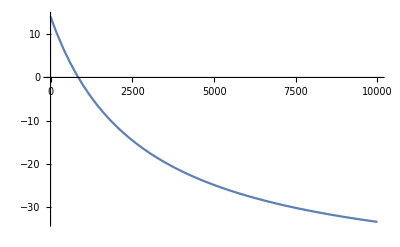

```mathematica
Plot[-46.80687987133107+171219.36050703155/(2810.240907767353+x),{x, 0 , 10000}]
```

```mathematica
Plot[171219/(2810.2409051125132+-46.806879857899425*x/1000)]
```

Plot::argr: 调用 Plot 时使用了 1 个参数；应该用 2 个参数.

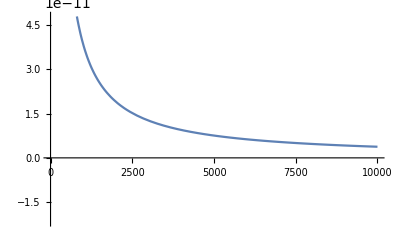

Plot::argr: 调用 Plot 时使用了 1 个参数；应该用 2 个参数.

Plot[e^x]

```mathematica
Plot[(-5.060935093003432*^-6)/(2810.2409051125132-(134297 x)/1000), {x, 0, 10000}]
```